```mathematica
数据输入
```

数据输入

```mathematica
Clear[data1K,data5K,data50,dataT];
data1K={{-111.1427,-98.9287,-86.9756,-75.2812,-63.8356,-52.6390,-41.6684,-30.9245,-20.3984,-10.0846,-0.0008,9.9058,19.6183,29.1433,38.4845,47.6410,56.6309,65.4537,74.1121,82.6119,90.9528},1000,2*1000,0.02};
data5K={{-111.1843,-98.9679,-87.0163,-75.3226,-63.8759,-52.6721,-41.7004,-30.9558,-20.4306,-10.1184,0.0006,9.9064,19.6188,29.1426,38.4838,47.6469,56.6358,65.4562,74.1143,82.6143,90.9584},5000,2*1000,0.02};
data50={{-110.9637,-98.7669,-86.8258,-75.1468,-63.7178,-52.5305,-41.5781,-30.8506,-20.3403,-10.0436,-0.0083,9.8964,19.5974,29.1126,38.4417,47.5912,56.5686,65.3396,74.0265,82.5149,90.8421},50,2*1000,0.02};
dataT={{20,2.4370},{25,2.4724},{30,2.5116},{35,2.5546},{40,2.5968},{45,2.6390},{50,2.6819},{55,2.7276},{60,2.7739},{65,2.8216},{70,2.8630},{75,2.9113},{80,2.9616},{85,3.0076}};
```

## 函数部分

```mathematica
Clear[dataprocessf1,dataprocessfT];
(*dataprocessf1是等臂非平衡电桥线性范围和灵敏度的处理*)
dataprocessf1[data_,R0_,Us_,steplength_]:=Module[{ndata,datapoints,tmpT,i,graphdata,dataf,graphdataerror1,graphdataerror2,dataintheoryf,graph1,graph2},
dataintheoryf[R_]:=(Us/4/R0)*(R-R0);
ndata=Dimensions[data][[1]];
tmpT=Table[R0+(i-(ndata+1)/2)*steplength*R0,{i,1,ndata}];
datapoints=Transpose[{tmpT,data}];
dataf=Interpolation[datapoints,InterpolationOrder->3,Method->"Spline"];
graphdata=ListPlot[datapoints];
graphdataerror1=ListPlot[Transpose[{Table[R0+(i-(ndata+1)/2)*steplength*R0,{i,1,(ndata-1)/2}],Table[Abs[(dataf[dR]-dataintheoryf[dR])/dataintheoryf[dR]],{dR,R0+(1-(ndata+1)/2)*steplength*R0,R0+((ndata-1)/2-(ndata+1)/2)*steplength*R0,steplength*R0}]}]];
graphdataerror2=ListPlot[Transpose[{Table[R0+(i-(ndata+1)/2)*steplength*R0,{i,(ndata+3)/2,ndata}],Table[Abs[(dataf[dR]-dataintheoryf[dR])/dataintheoryf[dR]],{dR,R0+((ndata+3)/2-(ndata+1)/2)*steplength*R0,R0+(ndata-(ndata+1)/2)*steplength*R0,steplength*R0}]}]];

graph1=Plot[{dataf[dR],dataintheoryf[dR]},{dR,R0+(1-(ndata+1)/2)*steplength*R0,R0+(ndata-(ndata+1)/2)*steplength*R0}];

graph2=Plot[{Abs[(dataf[dR]-dataintheoryf[dR])/dataintheoryf[dR]],0.05},{dR,R0+(1-(ndata+1)/2)*steplength*R0,R0+(ndata-(ndata+1)/2)*steplength*R0}];
(*输出部分，分别是理论线和实测线的图像，相对偏差的图像，相对偏差达到0.05时R的值，电桥的绝对灵敏度（mV/Omega）*)
{Show[graph1,graphdata,AxesLabel->{"R_4(Ω)","U_g(mV)"}],Show[graph2,graphdataerror1,graphdataerror2,AxesLabel->{"R_4(Ω)","δU_g"}],FindRoot[Abs[(dataf[R]-dataintheoryf[R])/dataintheoryf[R]]==0.05,{R,{R0+(1-(ndata+1)/2)*steplength*R0,R0+(ndata-(ndata+1)/2)*steplength*R0}}],(R/.FindRoot[Abs[(dataf[R]-dataintheoryf[R])/dataintheoryf[R]]==0.05,{R,{R0+(1-(ndata+1)/2)*steplength*R0,R0+(ndata-(ndata+1)/2)*steplength*R0}}])/R0,Us/4/R0}
];

dataprocessfT[data_,S_]:=Module[{kp,tpdata,tp,lm,x,fdata,t,n},
n=Dimensions[data][[1]];
fdata[t_]=Fit[data,{1,t},t];
lm=LinearModelFit[data,{x},{x}];
{lm["ParameterConfidenceIntervalTable",ConfidenceLevel->0.95],Show[ListPlot[data],Plot[fdata[t],{t,data[[1,1]],data[[n,1]]}],AxesLabel->{"T(°C)","U_g(mV)"}],lm["RSquared"]}
]
```

## 电阻为50, 1 K, 50 KΩ的等臂非平衡电桥的灵敏度、线性范围、图表（含误差曲线）

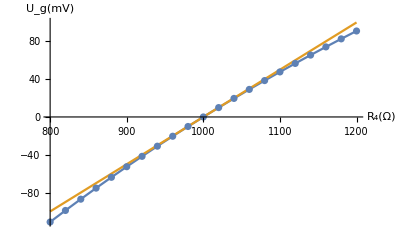

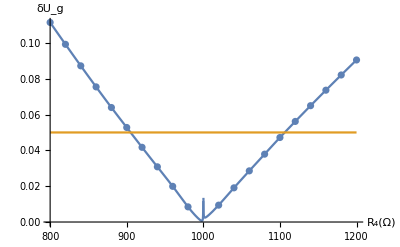

{R→{905.018,1106.22}}

{0.905018,1.10622}

1/2

```mathematica
dataprocessf1[data1K[[1]],data1K[[2]],data1K[[3]],data1K[[4]]][[1]]
dataprocessf1[data1K[[1]],data1K[[2]],data1K[[3]],data1K[[4]]][[2]]
dataprocessf1[data1K[[1]],data1K[[2]],data1K[[3]],data1K[[4]]][[3]]
dataprocessf1[data1K[[1]],data1K[[2]],data1K[[3]],data1K[[4]]][[4]]
dataprocessf1[data1K[[1]],data1K[[2]],data1K[[3]],data1K[[4]]][[5]]
```

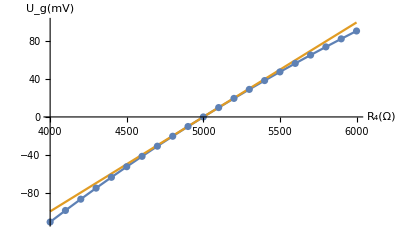

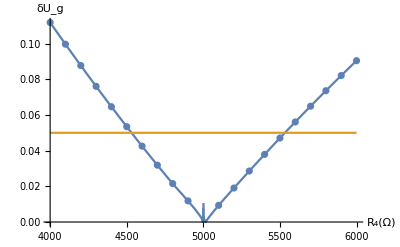

{R→{4531.26,5532.43}}

{0.906252,1.10649}

1/10

```mathematica
dataprocessf1[data5K[[1]],data5K[[2]],data5K[[3]],data5K[[4]]][[1]]
dataprocessf1[data5K[[1]],data5K[[2]],data5K[[3]],data5K[[4]]][[2]]
dataprocessf1[data5K[[1]],data5K[[2]],data5K[[3]],data5K[[4]]][[3]]
dataprocessf1[data5K[[1]],data5K[[2]],data5K[[3]],data5K[[4]]][[4]]
dataprocessf1[data5K[[1]],data5K[[2]],data5K[[3]],data5K[[4]]][[5]]
```

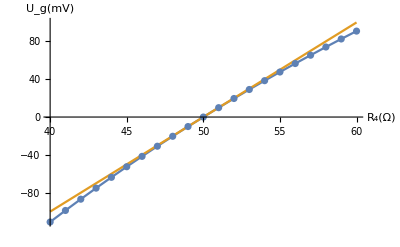

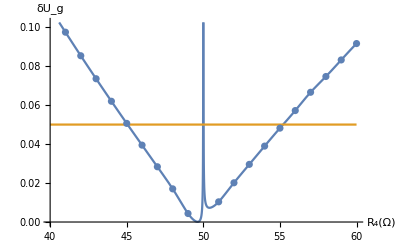

{R→{45.0543,55.2051}}

{0.901086,1.1041}

10

```mathematica
dataprocessf1[data50[[1]],data50[[2]],data50[[3]],data50[[4]]][[1]]
dataprocessf1[data50[[1]],data50[[2]],data50[[3]],data50[[4]]][[2]]
dataprocessf1[data50[[1]],data50[[2]],data50[[3]],data50[[4]]][[3]]
dataprocessf1[data50[[1]],data50[[2]],data50[[3]],data50[[4]]][[4]]
dataprocessf1[data50[[1]],data50[[2]],data50[[3]],data50[[4]]][[5]]
```

## 铜丝温度和电压关系图表、不确定度等计算

| Estimate | Standard Error | Confidence Interval
1 | 2.24689 | 0.00474749 | {2.23655,2.25724}
x$49873 | 0.00884813 | 0.0000844207 | {0.0086642,0.00903207}

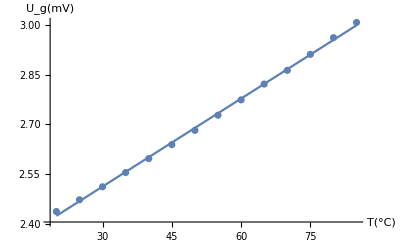

0.998909

```mathematica
dataprocessfT[dataT,0][[1]]
dataprocessfT[dataT,0][[2]]
dataprocessfT[dataT,0][[3]]
```

{{0,2.437},{5,2.4724},{10,2.5116},{15,2.5546},{20,2.5968},{25,2.639},{30,2.6819},{35,2.7276},{40,2.7739},{45,2.8216},{50,2.863},{55,2.9113},{60,2.9616},{65,3.0076}}

| Estimate | Standard Error | Confidence Interval
1 | 2.42386 | 0.00322847 | {2.41682,2.43089}
x$50191 | 0.00884813 | 0.0000844207 | {0.0086642,0.00903207}

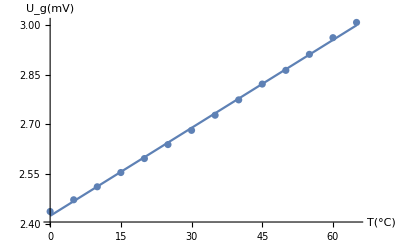

0.998909

```mathematica
Clear[dataT2];
dataT2=Transpose[{Transpose[dataT][[1]]-20,Transpose[dataT][[2]]}]
dataprocessfT[dataT2,0][[1]]
dataprocessfT[dataT2,0][[2]]
dataprocessfT[dataT2,0][[3]]
```